## MICA: Measurement, Instrumentation, Control & Analysis

## Geared Step Motor Demo

#### Ian Hunter, 3 March 2026

#### Revisions

2024		17	Sep	Started
2025		 3	Mar	Updated with new IMU mount (pointer)
2026		 2	Mar	Minor updates

#### Objectives

To write code to control a geared step motor (model 17HS13-0404S-PG5) such that it makes a 360 deg turn in 10 s while its angular position is measured every 50 ms (i.e., 20 Hz sampling rate) using an inertial measurement unit (IMU) attached to the gear box output shaft. The measured geared step motor angular position is then plotted as a function of time. Power is supplied by a small deWalt 20 V battery. A USB-c decoy is used to set the battery output to 12 V.

#### Keywords

Inertial Measurement Unit (IMU), Angular Position, Step Motor, Geared Step Motor, Gear Ratio, Silent Stepper Bricklet, Macro-Steps, Micro-Steps, Energy, Battery Energy, Voltage, Current, Power, USB-C Decoy.

#### Notes

Code that must be evaluated for the subsequent code to run properly starts with a black square (■). You click on this square to evaluate the adjacent code. All other code may be optionally evaluated in the usual way (Shift Enter or on a numerical key pad: Enter).

#### CAD Model

The OnShape CAD model shown above may be found at :
https://cad.onshape.com/documents/4fd3ede10e2749577871380a/w/1b1cb0c718af8125abbba1f5/e/a38fac108e36101a2612138f?renderMode=0&uiState=69a6068e2075f2734a47e6e6

#### Battery

We use a deWalt 20 V lithium ion battery. We need a source of power for the step motor separate from the USB-c connected to the Master Brick.  Part of the USB-c standard allows sources of electrical power such as batteries to deliver a specific voltage when requested. The device that does this is called a USB-c decoy. The one used here has 3 small switches (called DIP switches) which can be set to produce one of: 5, 9, 12, 15, and 20 V.  As mentioned we want 12 V.

Connect the power (adjacent red and black wires) to the Silent Stepper power input (black 2 wire connector).

We use either a deWalt Power Stack 20 V, 1.7 AH battery or a deWalt Power Stack 20 V, 5 AH battery. They both incorporate lithium ion prismatic (pouch) battery cells.
Lets calculate the energy stored by these batteries when fully charged (3 white LEDs showing when charge level button pushed).

#### 1.7 AH Battery

The designation of 1.7 amp hours (1.7 AH) is somewhat nominal. But if it was 1.7 AH = 1.7 A × 3600 s, then as power = Volts × Amps and energy = Watts × Seconds :

```mathematica
batteryVoltageV=20 Quantity[, "Volts"];
batteryAs= 1.7 Quantity[, "Amperes"] 3600 Quantity[, "Seconds"];
batteryEnergyJ=UnitConvert[batteryVoltageV batteryAs,"J"]
```

122400. J

This suggests that the battery will would store up to around 120 kJ of energy. 
However, the actual value is a little less. According to the value showed on the underside of the battery it can store 30.6 WH (Watt Hours) = 30.6 W × 3600 s:

```mathematica
batteryEnergyJ=30.6 Quantity[, "Watts"] × 3600 Quantity[, "Seconds"]
```

110160. s W

1 Watt × 1 Second = 1 Joule, so we have:

```mathematica
batteryEnergyJ=UnitConvert[30.6 Quantity[, "Watts"] × 3600 Quantity[, "Seconds"],"J"]
```

110160. J

So the battery when fully charged stores around 110 kJ.

The battery mass (including battery pouches, case and electronics) is:

```mathematica
batteryMasskg=0.3106 Quantity[, "Kilograms"];
```

So its mass energy density is:

```mathematica
batteryEnergyJ/batteryMasskg
```

354668. J/kg

For comparison a typical 12 V lead-acid car battery has an energy density of about 150 kJ/kg.

#### 5 AH Battery

The designation of 5 amp hours (5 AH) is somewhat nominal. But if it was 5 AH = 5 A × 3600 s, then as power = Volts × Amps and energy = Watts × Seconds :

```mathematica
batteryVoltageV=20 Quantity[, "Volts"];
batteryAs= 5 Quantity[, "Amperes"] 3600 Quantity[, "Seconds"];
batteryEnergyJ=UnitConvert[batteryVoltageV batteryAs,"J"]
```

360000 J

This suggests that the battery will would store up to around 360 kJ of energy. 
However, the actual value is a little less. According to the value showed on the underside of the battery it can store 90 WH (Watt Hours) = 90 W × 3600 s:

```mathematica
batteryEnergyJ=90.0 Quantity[, "Watts"] × 3600 Quantity[, "Seconds"]
```

324000. s W

1 Watt × 1 Second = 1 Joule, so we have:

```mathematica
batteryEnergyJ=UnitConvert[90.0 Quantity[, "Watts"] × 3600 Quantity[, "Seconds"],"J"]
```

324000. J

So the battery when fully charged stores around 324 kJ.

The battery mass (including battery pouches, case and electronics) is:

```mathematica
batteryMasskg=0.743 Quantity[, "Kilograms"];
```

So its mass energy density is:

```mathematica
batteryEnergyJ/batteryMasskg
```

436070. J/kg

Somewhat better than the smaller 1.7 AH battery. The difference in energy density is like mainly due to the packaging difference. The two battery chemistries are probably the same (i.e., the energy densities of the battery chemistry (without the packaging) is probably over 500 kJ/kg).

#### Connect to TinkerForge

```mathematica
"■";  (* Windows Only *)
Needs["NETLink`"];
LoadNETAssembly["Tinkerforge"];
```

```mathematica
"■";  (* Mac Only *)
(* for both Linux and Max OS need to load Mono from https://www.mono-project.com/download/stable/ *)
Needs["NETLink`"];
InstallNET["MonoPath"->"/Library/Frameworks/Mono.framework/Versions/Current/Commands/mono"];
LoadNETAssembly["Tinkerforge",NotebookDirectory[]];
```

```mathematica
"■";  host="localhost";
port=4223;
ipcon=NETNew["Tinkerforge.IPConnection"];
(* as usual you need to use the Brick Viewer to find the unique identifiers (UID) for each bricklet and insert below *)
imu=NETNew["Tinkerforge.BrickletIMUV3","ZoX",ipcon];
ss=NETNew["Tinkerforge.BrickletSilentStepperV2","25GL",ipcon];
ipcon@Connect[host,port];
```

#### Geared Step Motor Considerations

The geared step motor Model 17HS13-0404S-PG5 is manufactured by many companies. It has a nominal ratio between the input step motor and output planetary gear box of 5:1. This means that if the step motor shaft (internal to the unit) rotates by 5 revs then the  gear box output shaft rotates by 1 rev. 
However, this is the nominal value. The actual value is:

```mathematica
"■";  gearRatio=5.+2/11
```

5.18182

We will need this value in the code below.

The TinkerForge Silent Stepper Bricklet can drive a maximum current per phase of 1.6 A and a minimum voltage of 8 V and maximum of 46 V. We use 1.5 A and 12 V here. 
Like almost all step motors the one used here has 200 macro-steps per rev of the step motor before the gear box. The Silent Stepper Bricklet can interpolate between steps. These interpolated steps are often called micro-steps. The Silent Stepper Bricklet can produce 1, 2, 4, 8, 16, 32, 64, 128 or 256 micro-steps per macro step. So for example if we select 256 micro-step interpolation then we get 256 x 200 = 51,200 micro-steps per rev of the step motor before the gear box.

So the total number of micro-steps to produce 1 rev of the gear box output shaft is:

```mathematica
microStepsPerRev=256 200 gearRatio
```

265309.

We need this as an integer:

```mathematica
"■";  microStepsPerRev=Round[256 200 gearRatio]
```

265309

In the experiment below we want to produce 1 rev/10 s, so we need a velocity (see SetMaxVelocity[] below ) of:

```mathematica
(256 200 gearRatio)/10
```

26530.9

We will round this to the nearest integer (an integer is required by SetMaxVelocity[] command)

```mathematica
"■";  microStepsPerSec=26531
```

26531

When looking at the step motor from the front clockwise (CW) rotation is caused by -ve micro-steps and counter-clockwise (CCW) rotation is caused by +ve micro-steps
We need to tell the Silent Stepper how quickly to accelerate and decelerate. The maximum for both is:

```mathematica
2^16-1
```

65535

```mathematica
"■";  ss@SetMotorCurrent[1500]; (* 1500 mA *)
ss@SetStepConfiguration[Tinkerforge`BrickletSilentStepperV2`STEPURESOLUTIONU256,True];(* 256 micro-steps per macro-step *)
ss@SetSpeedRamping[60000,60000]; (* near the max for both *)
```

#### Check IMU Angle

Note that the imu returns angle with respect to the earth. It can only be considered to measure shaft angle if the geared step motor body remains fixed in space. So during the experiment below you need to make sure that the geared step motor shaft is vertical and the body does no move as its shaft rotates.
Manually rotate the step motor body (not just the shaft) until you get an angle of just below 0.0 (e.g., between 359.5 and 0.0 deg). Rerun this code until you get the angle just below 0.0:

```mathematica
"■";  
Do[
angle=0.0;
tmp1=0.0;
tmp2=0.0;
imu@GetOrientation[angle,tmp1,tmp2];
Print[angle/16.];
Pause[1],
15]
```

0.125

0.125

0.125

«3 more identical outputs»

359.688

359.688

359.688

«6 more identical outputs»

#### Experiment: Measure Gear Step Motor Output Shaft Angle as a Function of Time

We will rotate clockwise by 1 rev in about 10 s, then pause for about 2 s, then rotate counter-clockwise by 1 rev in about another 10 s. Note that we have to consider the effect of the acceleration and deceleration times.

```mathematica
"■"; 
n=460; (* this is the total number of samples and includes some extra samples to account for the acceleration and deceleration times *)
ss@SetMaxVelocity[microStepsPerSec]; (* velocity in micro-steps/s *)
ss@SetEnabled[True];(* enable motor power *)
Pause[0.1]; (* wait a little for the motor to turn on *)

time=Table[0,n];
angle=Table[0,n];
a=0.0;
b=0.0;
c=0.0;
δt=0.05; (* desired inter-sample interval in s *)
ti=0;
t0=AbsoluteTime[];
i=1;

(* Rotate CW by 1 rev in 10 s *)
ss@SetSteps[-microStepsPerRev] (* drive CW by 1 rev *)
Do[
While[(AbsoluteTime[]-t0)< δt(i-1)];
time[[i]]= AbsoluteTime[]-t0; 
imu@GetOrientation[a,b,c];
angle[[i]]=a/16.0;
i=i+1,
250]

(* rotate CCW by 1 rev in 10 s *)
ss@SetSteps[microStepsPerRev]; (* drive CCW by 1 rev *)
Do[
While[(AbsoluteTime[]-t0)< δt(i-1)];
time[[i]]= AbsoluteTime[]-t0; 
imu@GetOrientation[a,b,c];
angle[[i]]=a/16.0;
i=i+1,
210] (* take 10 more samples to account for acceleration and deceleration times *)

Pause[2]; (* wait a little as it is not good to disable the step motor while it is moving *)
ss@SetEnabled[False]; (* disable motor power *)
```

1

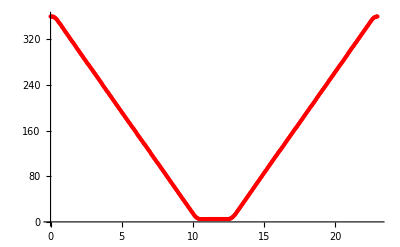

```mathematica
"■";  ListPlot[{time,angle}ᵀ,PlotStyle->Red]
```

Lets re-plot with title and axis labels:

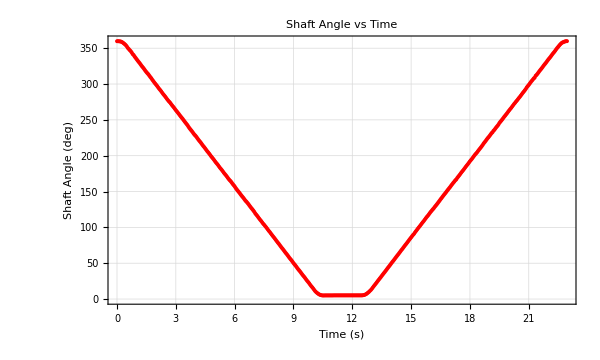

```mathematica
"■";  
ListPlot[{time,angle}ᵀ,
PlotRange->All,PlotStyle->Red,
PlotTheme->{"Scientific","Grid"},PlotMarkers->{Automatic,Tiny},
PlotLabel->Style["Shaft Angle vs Time",FontFamily->"Times",FontSize->18,Bold,Black],
FrameLabel->{Style["Time (s)",FontFamily->"Times",FontSize->16,Bold,Black],Style["Shaft Angle (deg)",FontFamily->"Times",FontSize->16,Bold,Black]},
LabelStyle->Directive[Black,FontFamily->"Times",FontSize->14],
PlotLabels->None,AspectRatio->0.6,ImageSize->600]
```

Note that the acceleration and deceleration phases in the plot are clearly visible.

#### Store Data

By default Wolfram does not store data. We can use the following to store our measurements.

```mathematica
"■";  PersistentSymbol["GearedStepMotorDemoData"]={time,angle};
```